What is used in this document:

1. Taylor expansion of variables of comparable norm: e.g. FradialForm
2. Simple Matrix Algebra: calculateHMatrix
3. Writing complex expressions in (complex) radial form: e.g.  FradialForm
4. Careful manipulations involving the arctan function: arctan
5. Making variable substitutions to simplify expressions: e.g.  calculating H21

## Function Definitions

```mathematica
(*This is an initialization cell*)
Clear["Global`*"] (*Clear Previous History*)

(*Useful Functions to use*)
absArgForm[complexExpr_,exactSolve_]:=Module[{exprArg,exprNorm},
absArgtemp1=Simplify[Re[ComplexExpand[complexExpr]]];
absArgtemp2=Simplify[Im[ComplexExpand[complexExpr]]];

exprNorm = Simplify[Sqrt[absArgtemp1^2+absArgtemp2^2]];

If[exactSolve== True,

(*Exact equations*)
absArgtemp1= FullSimplify[absArgtemp1/exprNorm];
absArgtemp2=FullSimplify[absArgtemp2/exprNorm];
absArgtemp1=Simplify[Reduce[
{Cos[exprArg]==absArgtemp1,
Sin[exprArg]==absArgtemp2,
-Pi<exprArg<Pi},exprArg]];

absArgtemp1=Solve[absArgtemp1,exprArg]; 
exprArg=exprArg/.absArgtemp1[[1]],

(*Looser Conditions*)
exprArg = ArcTan[absArgtemp2/absArgtemp1];
exprArg=exprArg+FullSimplify[ If[absArgtemp1 < 0, 
FullSimplify[If[absArgtemp2<0,-Pi,Pi]],
0] ];	

];

(*Return Expression in vector form: {Norm*Exp[I*Argument], Norm, Argument}*)
{exprNorm*Exp[I*exprArg],exprNorm,exprArg}
]

(* Will be useful for making simplications later on; taken from http://stackoverflow.com/questions/8073530/get-mathematica-to-simplify-expression-with-another-equation *)
replacementFunction[expr_,rep_,vars_]:=Module[{num=Numerator[expr],den=Denominator[expr],hed=Head[expr],base,expon},If[PolynomialQ[num,vars]&&PolynomialQ[den,vars]&&!NumberQ[den],replacementFunction[num,rep,vars]/replacementFunction[den,rep,vars],If[hed===Power&&Length[expr]==2,base=replacementFunction[expr[[1]],rep,vars];expon=replacementFunction[expr[[2]],rep,vars];PolynomialReduce[base^expon,rep,vars][[2]],If[Head[hed]===Symbol&&MemberQ[Attributes[hed],NumericFunction],Map[replacementFunction[#,rep,vars]&,expr],PolynomialReduce[expr,rep,vars][[2]]]]]]
```

## The Derivation

### Assumptions + Variable Definitions

```mathematica
(*Assumptions made throughout the document*)
$Assumptions={x>0,R>0,T>0, T<1, I0>0,ω0>0,m>0,c>0, Ω>0,T+R==1, L>0, τ>0, ξ>0, κ>0,gSQL>0};

(*Symbolic definitions*)
s=-1;
R = 1-T;
χ=Exp[I*x];  (*x = Ωτ*) (*τ = L/c;*)
MMatrix = χ^2*{{1, 0}, {s*4*κ/T, 1}}; (*κ=8*I0*ω0/m/c^2/Ω^2;*)
(*gSQL = Sqrt[2*ℏ*m*Ω^2];*)
Dvec=-χ/gSQL*{0,Sqrt[2*κ*(4/T)]};

(*Simplfying assignments that will be used*)
repSimplify1=Numerator[Together[φ-T/4/x]];
repCavityBandwith=Numerator[Together[γ-T*c/(4*L)]];
repPhi=Numerator[Together[ξ-Ω/γ]]; (*ξ = Ω/γ > 0*)
```

### Step 1: Calculate H̲ Matrix

```mathematica
(*Begin Matrix Algebra*)
PMatrix = FullSimplify[Inverse[MMatrix] - Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[T*Inverse[PMatrix]-Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[HMatrix];

HMatrix//MatrixForm (*Result of algebra*)
```

((-2+T+2 √(1-T) Cos[2 x])/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x]) | 0
(4 κ)/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x]) | (-2+T+2 √(1-T) Cos[2 x])/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x]))

```mathematica
(*Other equivalent but simpler approach*)
HMatrix = T*Inverse[IdentityMatrix[2]-Sqrt[R]*MMatrix].MMatrix;
HMatrix = FullSimplify[HMatrix-Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[HMatrix];

HMatrix//MatrixForm (*Result of algebra*)
```

((-ⅇ^(2 ⅈ x)+√(1-T))/(-1+ⅇ^(2 ⅈ x) √(1-T)) | 0
-(4 ⅇ^(2 ⅈ x) κ)/((-1+ⅇ^(2 ⅈ x) √(1-T))^2) | (-ⅇ^(2 ⅈ x)+√(1-T))/(-1+ⅇ^(2 ⅈ x) √(1-T)))

#### Observations on the calculated H̲ Matrix

Observations:H_12=0
H_11=H_22
H_21=-(ⅇ^(2 ⅈ x) T κ)/((-1+ⅇ^(2 ⅈ x) √(1-T))^2)
=-(ⅇ^(2 ⅈ x) T κ)/((-ⅇ^(2 ⅈ x)+√(1-T))(-1+ⅇ^(2 ⅈ x) √(1-T)))(-ⅇ^(2 ⅈ x)+√(1-T))/(-1+ⅇ^(2 ⅈ x) √(1-T))
=H_11(ⅇ^(2 ⅈ x) T κ)/((-ⅇ^(2 ⅈ x)+√(1-T))(-1+ⅇ^(2 ⅈ x) √(1-T)))
=H_11(T κ)/((-1+ⅇ^(-2 ⅈ x)√(1-T))(-1+ⅇ^(2 ⅈ x) √(1-T)))
=H_11(T κ)/((|-1+ⅇ^(2 ⅈ x) √(1-T)|)^2)=H_11×RealNumber

Moreover, both approaches are indeed the same:

```mathematica
FullSimplify[({{(-ⅇ^(2 ⅈ x)+√(1-T))/(-1+ⅇ^(2 ⅈ x) √(1-T)), 0}, {-(4 ⅇ^(2 ⅈ x) κ)/((-1+ⅇ^(2 ⅈ x) √(1-T))^2), (-ⅇ^(2 ⅈ x)+√(1-T))/(-1+ⅇ^(2 ⅈ x) √(1-T))}})-({{(-2+T+2 √(1-T) Cos[2 x])/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x]), 0}, {(4 κ)/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x]), (-2+T+2 √(1-T) Cos[2 x])/(2 √(1-T)+(-2+T) Cos[2 x]+ⅈ T Sin[2 x])}})]//MatrixForm
```

(0 | 0
0 | 0)

### Step 2: Make approximations (because T and x are of comparable small norm) to simplify the H̲ Matrix

#### HMatrix is a lower triangular Try to first simplify the diagonal terms -which are identical- by writing them in radial form.

```mathematica
HMatrix11=Series[HMatrix[[1,1]]/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,0}];
HMatrix11 = Simplify[Normal[HMatrix11]];
HMatrix11 = HMatrix11/.{ϵ-> 1}

(absArgForm[HMatrix11,False])[[1]] (*Subscript[H, 11] in  radial form*)
```

(T+4 ⅈ x)/(T-4 ⅈ x)

ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T<4 x}, {0, True}}])))

#### Try to simplify the argument by using a different strategy: try to reduce the number of variables to 1

```mathematica
HMatrix11=FullSimplify[HMatrix11];
HMatrix11=Simplify[replacementFunction[HMatrix11,repSimplify1,{x, T}]] ;(*Replace T/4x by φ*)

(*Now that the we have reduced the expression to one parameter (that is positive and so does not have any weird conditions on it), try to write it in abs arg form again*)
Simplify[ Assuming[ φ>0,(absArgForm[HMatrix11,False])[[3]] ] ]
```

ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])

#### Use ArcTan Identities to simplify the above expression

From (http://en.wikipedia.org/wiki/Inverse_trigonometric_functions#Arctangent_addition_formula), we have that

2tan^-1(u)=tan^-1((2u)/(1-u^2))[Mod π]

The Mod π is because tan^-1 is defined over the domain [-π/2, π/2]. Hence,

ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])=-ArcTan[(2 φ)/(1-φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+(Piecewise[{{π, φ<1}, {0, True}}])+Mod[π]

When is |-2 tan^-1 u|>π/2? First, we note that φ>0 so that | -2 tan^-1 φ |=| 2 tan^-1 φ |=2 tan^-1 φ  (because the inverse tangent of a positive number is positive). We ask when is tan^-1 φ>π/4?

```mathematica
Simplify[Reduce[ArcTan[φ]> π/4,φ]]
```

φ>1

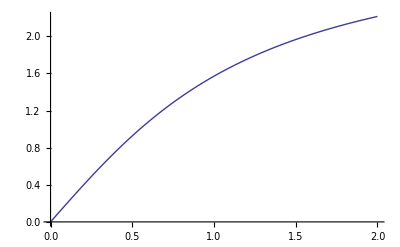

```mathematica
(*Visual representation for verification purposes*)
Plot[{2*ArcTan[φ]},{φ,0,2},
AxesLabel-> {φ}]
```

Hence, when φ>1, -2ArcTan[φ]<-π/2 and so we have to add π to remedy the issue: we obtain that ArcTan[(2 φ)/(-1+φ^2)]=-2ArcTan[φ]+(Piecewise[{{0, φ<1}, {π, φ>1}}])
⟹ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])=-2ArcTan[φ]+(Piecewise[{{0, φ<1}, {π, φ>1}}])+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+π

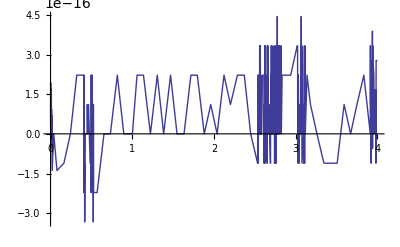

```mathematica
(*Visual representation for verification purposes*)
Plot[(ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])-(π-2*ArcTan[φ])),{φ,0,4},
AxesLabel-> {φ}]
```

Finally,we use the identity that arctan(1/x)=-π/2-arctan(x) to obtain that:


H_11=ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T<4 x}, {0, True}}])))
=ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+π
=2(π/2-ArcTan[φ])=2ArcTan[1/φ]
=2ArcTan[(4x)/T]
⇒H_11=H_22=(T+4 ⅈ x)/(T-4 ⅈ x)=exp(2ⅈArcTan[(4x)/T])
=e^(2ⅈϕ), 
where ϕ≡ArcTan[(4x)/T]

```mathematica
(*Side Note: This could have also worked*)

Series[HMatrix[[1,1]]/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,0}];

Simplify[Normal[%]];
Simplify[%/.{x-> Ω*(L/c)}];
Simplify[replacementFunction[%,repCavityBandwith,{c, T, L}]];
temp = Simplify[replacementFunction[%,repPhi,{Ω, γ}]];

HMatrix11absArgForm = (absArgForm[temp,True])[[1]]
```

ⅇ^(2 ⅈ ArcTan[ξ])

#### Simplify the off-diagonal term by making use of approximations: H_21

```mathematica
HMatrix21= HMatrix[[2,1]];

(*Find the lowest order term*)
Manipulate[Normal[Series[HMatrix21/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,o}]],{o,-10,10,1}]
```

```mathematica
(*-1 is our winner*)
HMatrix21 = Series[HMatrix[[2,1]]/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-2}];
HMatrix21 = Simplify[Normal[HMatrix21]];
HMatrix21 = Simplify[HMatrix21/.{ϵ-> 1}];

(*Try the radial form to see if it is simple*)
Simplify[(absArgForm[HMatrix21,False])[[1]]]
```

(16 ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{-π, T>4 x}, {0, True}}]))) κ)/(T^2+16 x^2)

The argument of the above expression can be written

ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{-π, T>4 x}, {0, True}}])))=ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T>4 x}, {0, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{2π, T>4 x}, {π, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{0, T>4 x}, {π, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{0, T>4 x}, {π, T<4x}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T<4 x}, {0, True}}])))
=-H_11=exp(2ⅈArcTan[(4x)/T])
The last equality comes from using result H11

⟹H_21~T_0(H_11)(-(4  T κ)/(T^2+16 x^2))
where T_0(H_11) is the Taylor expansion of H_11 up to zeroth order.

Now we work on rewriting -(4  T κ)/(T^2+16 x^2) in terms of physical variables:

-(4   κ)/(T^2+16 x^2)=-(4   κ)/(T^2+16 x^2)
=-1/(T^2+16 x^2)4(8 I_0 ω_0)/(mc^2 Ω^2)=-1/(T^2+16 x^2)TL/cΩ^2(8(4I_0/T)ω_0)/mLc
=-T/(Ω^2(T^2+16 Ω^2 τ^2))τ(8 I_c ω_0)/mLc=-Tτι_c/(Ω^2(T^2+16 Ω^2 τ^2))
=-Tτι_c/(16 τ^2 Ω^2((T/4τ)^2+Ω^2))=-((T/4τ)ι_c)/(4Ω^2((T/4τ)^2+Ω^2))
=-(γ×ι_c)/(4Ω^2(γ^2+Ω^2))=-1/8(2γ×ι_c)/(Ω^2(γ^2+Ω^2))

Hence, using result H11
H_21=-e^(2ⅈϕ)4(4   κ)/(T^2+16 x^2)
=-e^(2ⅈϕ)1/2(2γ×ι_c)/(Ω^2(γ^2+Ω^2))

#### Simplify the off-diagonal term by making use of approximations (the better way): H_21

Use the observations exact observations that H_21∝H_11 and the constant of proportionality is real

```mathematica
H21DivH11= HMatrix[[2,1]]/HMatrix[[1,1]];

H21DivH11 = Series[H21DivH11/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-2}];
H21DivH11 = FullSimplify[Normal[H21DivH11]];
H21DivH11 = FullSimplify[H21DivH11/.{ϵ-> 1}];

H21DivH11=Simplify[H21DivH11/.{κ-> 8*I0*ω0/m/c^2/Ω^2,x-> Ω*L/c}];

H21DivH11=Simplify[replacementFunction[H21DivH11,repCavityBandwith,{c, T, L}]]

varChangeω0=ω0/.(Solve[ι==8*ω0*(4*I0/T)/(L*c*m),ω0])[[1]];
H21DivH11=Simplify[H21DivH11/.{ω0-> varChangeω0}]

H21DivH11=Simplify[replacementFunction[H21DivH11,repCavityBandwith,{c, T, L}]]
```

-(8 I0 ω0)/(L^2 m Ω^2 (γ^2+Ω^2))

-(c T ι)/(4 L γ^2 Ω^2+4 L Ω^4)

-(γ ι)/(γ^2 Ω^2+Ω^4)

Hence, we obtain (using result H11) that H_21/H_11=-1/2(2 γ ι)/(Ω^2 (γ^2+Ω^2))+O(0)
⟹H_21=-e^(2ⅈϕ)1/2(2 γ ι)/(Ω^2 (γ^2+Ω^2))+O(0)
which is the same as result1 H22.

### Step3: Calculate F⃗

```mathematica
Fvec=Sqrt[T]*Inverse[IdentityMatrix[2]-MMatrix*Sqrt[R]].Dvec;
Fvec=Simplify[Fvec];

Fvec //MatrixForm
```

(0
-(2 √2 ⅇ^(ⅈ x) √κ)/(gSQL-ⅇ^(2 ⅈ x) gSQL √(1-T)))

#### Observations on calculated F⃗ matrix

```mathematica
Simplify[Im[ComplexExpand[Fvec[[2]]]]]
```

(√2 (1+√(1-T)) √κ Sin[x])/(gSQL (-2+T+2 √(1-T) Cos[2 x]))

Observations:
 F⃗ is definitely not real valued. 
 F⃗ is of the form(0
F_2)

### Step4: Use that T and x are of small comparable norm to make simplifications

#### Try to write F⃗ in radial form

```mathematica
Fvec2= Fvec[[2]];

(*Find the lowest order term*)
Manipulate[Normal[Series[Fvec2/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,o}]],{o,-10,10,1}]
```

```mathematica
(*-1 is our winner*)
Fvec2= Fvec[[2]];

Fvec2 = Series[Fvec2/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-1}];
Fvec2 = Simplify[Normal[Fvec2]];
Fvec2 = Simplify[Fvec2/.{ϵ-> 1}];

(absArgForm[Fvec2,False])[[1]]
```

(4 √2 ⅇ^(ⅈ (-π+ArcTan[(4 x)/T])) √(κ/(T^2+16 x^2)))/gSQL

We remember the definition  ϕ≡ArcTan[(4x)/T] (result1 H22). Further, 
-g_SQL×F_2=4 √2 ⅇ^ⅈϕ √(κ/(T^2+16 x^2))
=4 √2 ⅇ^ⅈϕ √(1/(4T)(4Tκ)/(T^2+16 x^2))
=4 √2 ⅇ^ⅈϕ √(1/(4T)T/8(2γ×ι_c)/(Ω^2(γ^2+Ω^2)))
= ⅇ^ⅈϕ √((2γ×ι_c)/(Ω^2(γ^2+Ω^2)))
where we used result1 H22 in the third equality.

Hence, F_2=-ⅇ^ⅈϕ 1/g_SQL √((2γ×ι_c)/(Ω^2(γ^2+Ω^2))). Using observations Fvector, we can now write that F⃗=-(0
ⅇ^ⅈϕ 1/g_SQL √((2γ×ι_c)/(Ω^2(γ^2+Ω^2)))).